```mathematica
Limit[(Sin [x])/x,x-> 0]
```

1

```mathematica
Limit[(Abs [x-a])/(x-a),x-> a]
```

1

```mathematica
lh1=Limit[Abs[x]/x,x-> 0,Direction->1]
rh1=Limit[Abs[x]/x,x-> 0,Direction->-1]
```

-1

1

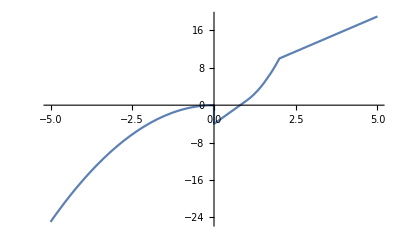

```mathematica
(*Example-14: A function f(x) is defined as follows:*)
(*f(x)=-x^2     :  x≤ 0
    =5x-4    : 0<x≤ 1
   =4 x^2-3x  : 1<x<2
  =3x+4    : x≥ 2
Test  the continuity of f(x) at x=0,1,2.
*)
Clear [f]
f[x_]:=-x^2/;x≤ 0
f[x_]:=5x-4/;0<x≤ 1
f[x_]:=4 x^2-3x/;1<x<2
f[x_]:=3x+4/;x≥ 2
Plot[f[x],{x,-5,5}]
```

```mathematica
lh1=Limit[-x^2,x-> 0,Direction->1];
rh1 =Limit[5x-4,x-> 0,Direction-> -1];
f[0];
lh1==rh1==f[0]
```

False

```mathematica
lh1 =Limit[5x-4,x-> 1,Direction-> 1];
rh1 =Limit[4 x^2-3x,x-> 1,Direction-> -1]; 
f[1];
lh1==rh1==f[1]
```

True

```mathematica
lh1 =Limit[4 x^2-3x,x-> 2,Direction-> 1];
rh1 =Limit[3x+4,x-> 2,Direction-> -1]; 
f[2];
lh1==rh1==f[2]
```

True

```mathematica
(*f(x) is continuous at x=1 and x=2.*)
(*Example-15 Show that the funtion f(x) defined by
f(x)= x^2 Sin[1/x] if x≠ 0
f(x)= 0 if x=0
is differentiable everywhere. Discuss also the continuity of the derivative f'(x).
*)
Clear[f,lhd,rhd,lh1,rh1]
f[x_]=x^2 Sin[1/x];
f'[x]
-Cos[1/x]+2x Sin[1/x]
f[0]=0;
lhd=Limit[(f[0-h]-f[0])/-h,h-> 0];
rhd=Limit[(f[0+h]-f[0])/h,h-> 0];
lhd==rhd
```

-Cos[1/x]+2 x Sin[1/x]

-Cos[1/x]+2 x Sin[1/x]

True

```mathematica
lh11=Limit[f'[x],x-> 0,Direction-> 1]
```

Interval[{-1,1}]

```mathematica
(*Example-16: Show that f(x)=x tan^-1(1/x) for x≠0 and f(0)=0 is not differentiable at x=0*)
Clear[f,lhd,rhd];
f[x_]=x*ArcTan[1/x];
```

```mathematica
(*if after x we don't put * then it will not give right answer*)
f[0]=0;
lhd=Limit[(f[0-h]-f[0])/-h,h-> 0];
rhd=Limit[(f[0+h]-f[0])/h,h-> 0];
lhd==rhd
```

False

```mathematica
(*Example-17. Show that the function defined by f(x)=|x|+|x-1| is continuous but not differentiable at x=0 and x=1.*)
```

```mathematica
Clear[f,lh1,rh1,lhd,rhd];
f[x_]=Abs[x]+Abs[x-1];
lh1=Limit[f[x],x-> 0,Direction-> 1]
rh1 = Limit[f[x],x-> 0,Direction-> -1]
f[0]
lh1==rh1==f[0]
```

1

1

1

True

```mathematica
(*Hence the given function is continuous at x=0 and for x=1*)
Clear[f,lh1,rh1,lhd,rhd];
f[x_]=Abs[x]+Abs[x-1];
lhd=Limit[(f[0-h]-f[0])/-h,h-> 0];
rhd=Limit[(f[0+h]-f[0])/h,h-> 0];
lhd==rhd
```

False

```mathematica
(*
Find the derivative of f(x)= x^5+x^4+x^3+x^2+x+1 in different way
*)
f[x_]= x^5+x^4+x^3+x^2+x+1;
f'[x]
```

1+2 x+3 x^2+4 x^3+5 x^4

```mathematica
f''[x]
```

2+6 x+12 x^2+20 x^3

```mathematica
D[x^5+x^4+x^3+x^2+x+1,x]
```

1+2 x+3 x^2+4 x^3+5 x^4

```mathematica
D[x^5+x^4+x^3+x^2+x+1,{x,2}]
```

2+6 x+12 x^2+20 x^3

```mathematica
D[(x^5+x^4+x^3+x^2+x+1), x]
```

1+2 x+3 x^2+4 x^3+5 x^4

```mathematica
D[(x^5+x^4+x^3+x^2+x+1), {x,2}]
```

2+6 x+12 x^2+20 x^3

```mathematica
D[(x^5+x^4+x^3+x^2+x+1), {x,4}]
```

24+120 x

```mathematica
D[(x^5+x^4+x^3+x^2+x+1), {x,5}]
```

120

```mathematica
Derivative[1][f][x]
```

1+2 x+3 x^2+4 x^3+5 x^4

```mathematica
Derivative[2][f][x]
```

2+6 x+12 x^2+20 x^3

```mathematica
Derivative[4][f][x]
```

24+120 x

```mathematica
Derivative[5][f][x]
```

120

-x^3+√(5+x^6)

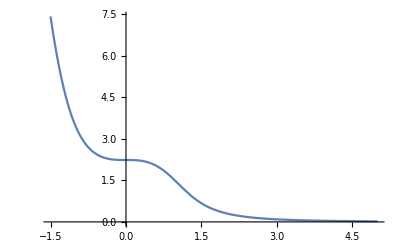

```mathematica
(*
Example-27.
Let f(x) = √(x^6+5)-x^3
(a) Plot the graph of f on the interval [-1.5,5]
(b) Find the limit of f at infinity
(c) Find f'(x) and f''(x) directly. Plot the graphs of f'(x) and f''(x) in different colors in the same set f axes.
*)
f[x_]= √(x^6+5)-x^3
Plot[f[x],{x,-1.5,5}]
```

```mathematica
Limit[f[x],x-> Infinity,Direction->1 ]
```

0

```mathematica
Limit[f[x],x-> Infinity,Direction->-1 ]
```

0

```mathematica
g=f'[x]
```

-3 x^2+(3 x^5)/(√(5+x^6))

```mathematica
h=f''[x]
```

-6 x-(9 x^10)/((5+x^6)^(3/2))+(15 x^4)/(√(5+x^6))

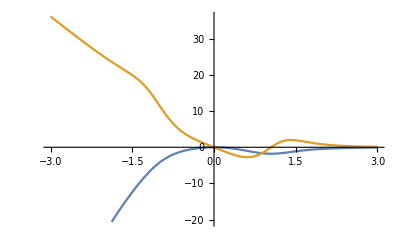

PlotStyle→{-Graphics-,-Graphics-}

```mathematica
Plot[{g,h},{x,-3,3}]
PlotStyle-> {RGBColor[1,0,0],RGBColor[0,1,0]}
```

```mathematica
(*
Example-30.
Find the values of c guaranteed Rolle's Theorem for the function f(x)=4x+39 x^2-46 x^3+17 x^4-2 x^5 on the interval [0,4].
*)
```

```mathematica
f[x_]=4x+39 x^2-46 x^3+17 x^4-2 x^5
f[0]
```

4 x+39 x^2-46 x^3+17 x^4-2 x^5

0

```mathematica
f[4]
```

0

```mathematica
NSolve[f'[c]==0](*Since f is polynomial so NSolve*)
```

{{c→-0.0472411},{c→1.05962},{c→2.27466},{c→3.51296}}

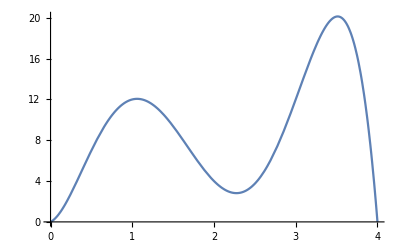

```mathematica
Plot[f[x],{x,0,4}]
```

```mathematica
(*
Example-31
Verify Roll's theorem for f(x)=2 x^3+x^2-4x-2 over the interval [-√2,√2].
*)
```

```mathematica
f[x_]=2 x^3+x^2-4x-2;
f[-√2]==f[√2]
```

True

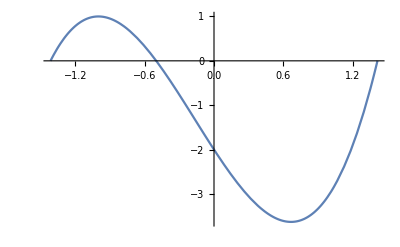

```mathematica
Plot[f[x],{x,-√2,√2}]
```

```mathematica
NSolve[f'[c]==0]
```

{{c→-1.},{c→0.666667}}

```mathematica
(*
Example-32. Verify Rolle's theorem for the following function.
(i) f(x)=e^-x sin x in the interval (0,Pi)
(ii) f(x)=x^2-3x+2 in the interval (1,2)
(iii) f(x) = (x-2)(x-3)(x-4) in the interval (2,3)
*)
```

```mathematica
(*i*)
f[x_]=e^-x *Sin [x] ;
f[0]==f[Pi]
```

True

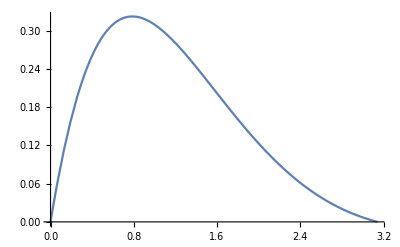

```mathematica
Plot[f[x],{x,0,Pi}]
```

```mathematica
NSolve[f'[c]==0]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-2.35619},{c→0.785398}}

```mathematica
(*ii & iii try yourself*)
```

```mathematica
(*
Example-33
Find the values ,c guaranteed by the Mean value theorem for the function f(x)=√x+sin 2*Pi*x on the interval [0,2]. 
*)
```

Set::write: Tag Plus in (-3\ x^2 + 3\ x^5/√5 + x^6)[x] is Protected.

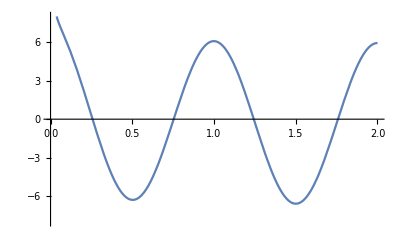

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-2.35619},{c→0.785398}}

```mathematica
f[x_]=√x+Sin [2*Pi*x];
a = 0; b= 2;
m = (f[b]-f[a])/(b-a);
g[x]=f[a]+m(x-a);
Plot[f'[x]-m,{x,0,2},PlotRange->{-8,8}]
```

```mathematica
sol1 = FindRoot[f'[c]==m,{c,.3}]
```

{c→0.257071}

```mathematica
sol2 = FindRoot[f'[c]==m,{c,.7}]
```

{c→0.753319}

```mathematica
sol3 = FindRoot[f'[c]==m,{c,1.3}]
```

{c→1.24344}

```mathematica
sol4 = FindRoot[f'[c]==m,{c,1.7}]
```

{c→1.75836}

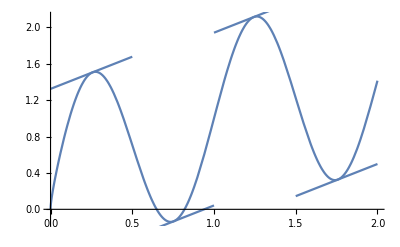

```mathematica
Subscript[a, 1]=sol1[[1,2]];
Subscript[a, 2]=sol2[[1,2]];
Subscript[a, 3]=sol3[[1,2]];
Subscript[a, 4]=sol4[[1,2]];
tan1[x_]=f[Subscript[a, 1]]+f'[Subscript[a, 1]](x-Subscript[a, 1])//Simplify;
tan2[x_]=f[Subscript[a, 2]]+f'[Subscript[a, 2]](x-Subscript[a, 2])//Simplify;
tan3[x_]=f[Subscript[a, 3]]+f'[Subscript[a, 3]](x-Subscript[a, 3])//Simplify;
tan4[x_]=f[Subscript[a, 4]]+f'[Subscript[a, 4]](x-Subscript[a, 4])//Simplify;
g1=Plot[{f[x],g[x]},{x,0,2},DisplayFunction->Identity];
g2=Plot[tan1[x],{x,0,0.5},DisplayFunction->Identity];
g3=Plot[tan2[x],{x,0.5,1},DisplayFunction->Identity];
g4=Plot[tan3[x],{x,1,1.5},DisplayFunction->Identity];
g5=Plot[tan4[x],{x,1.5,2},DisplayFunction->Identity];
Show[{g1,g2,g3,g4,g5},DisplayFunction->$DisplayFunction]
```